# Exercise 5.2

### task a)

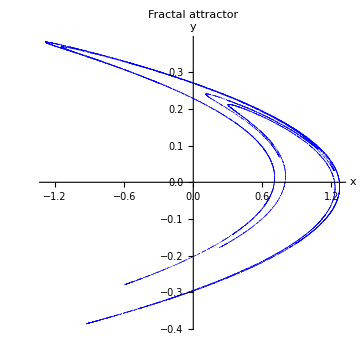

```mathematica
ClearAll["Global`*"]
a=1.4;
b=0.3;
iterations=100000;
transient=5000;

initialConditions={{0,0},{0.1,0},{0,0.1},{-0.1,0},{0,-0.1},{0.2,0.2},{-0.2,-0.2}};

HenonMap[{x_,y_}]:={y+1-a x^2,b x};

allPoints=Flatten[Table[NestList[HenonMap,init,iterations][[transient;;]],{init,initialConditions}],1];

subsetPoints=RandomSample[allPoints,15000];

(*Due to large file, dont plot all points!*)
ListPlot[subsetPoints,
AspectRatio->1,
AxesLabel->{"x","y"},
PlotStyle->{Blue,PointSize[0.001]},
PlotRange->All,
ImageSize->Medium,
PlotLabel->"Fractal attractor"]
```

### task b)

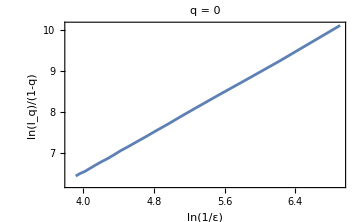

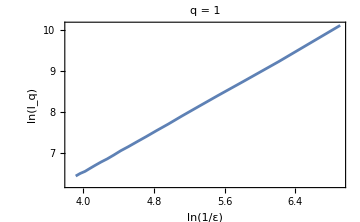

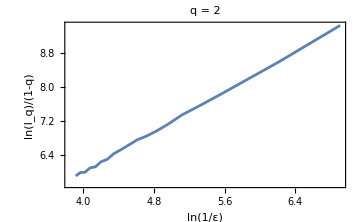

```mathematica
ClearAll["Global`*"]

a=1.4;
b=0.3;
iterations=2*10^6;
transient=5000;
eps=Range[0.001,0.02,0.001]; 

HenonMap[{x_,y_}]:={y+1-a x^2,b x};

data=NestList[HenonMap,{0.1,0.1},iterations][[transient;;]];
x=data[[All,1]];
y=data[[All,2]];

I0=ConstantArray[0,Length[eps]];
I1=ConstantArray[0,Length[eps]];
I2=ConstantArray[0,Length[eps]];

xmin=Round[Min[x],0.1];
xmax=Round[Max[x],0.1];
ymin=Round[Min[y],0.1];
ymax=Round[Max[y],0.1];

Do[e=eps[[i]];
bins=BinCounts[data,{xmin,xmax,e},{ymin,ymax,e}  ];
P=Flatten[bins];
P=Select[P,#>0&];
P=P/Total[P];
I0[[i]]=Total[P^0];
I1[[i]]=Total[(1/P)^P];
I2[[i]]=Total[P^2];
,
{i,Length[eps]}];

logInvEpsilon=Log[1/eps];

q0Plot=ListLinePlot[Transpose[{logInvEpsilon,Log[I0]}],
PlotLabel->"q = 0",
Frame->True,
FrameLabel->{"ln(1/ε)","ln(I_q)/(1-q)"},
ImageSize-> Medium]
q1Plot=ListLinePlot[Transpose[{logInvEpsilon,Log[I1]}],
PlotLabel->"q = 1",
Frame->True,
FrameLabel->{"ln(1/ε)","ln(I_q)"},
ImageSize-> Medium]
q2Plot=ListLinePlot[Transpose[{logInvEpsilon,-Log[I2]}],
PlotLabel->"q = 2",
Frame->True,
FrameLabel->{"ln(1/ε)","ln(I_q)/(1-q)"},
ImageSize-> Medium]
```

### task c)

```mathematica
ClearAll[modelD0,modelD1,modelD2,D0,D1,D2,x];

modelD0=LinearModelFit[Transpose[{logInvEpsilon,Log[I0]}],x,x];
modelD1=LinearModelFit[Transpose[{logInvEpsilon,Log[I1]}],x,x];
modelD2=LinearModelFit[Transpose[{logInvEpsilon,-Log[I2]}],x,x];

D0=modelD0["BestFit"][[2]]
D1=modelD1["BestFit"][[2]]
D2=modelD2["BestFit"][[2]]
```

1.23212 x

1.22867 x

1.18066 x

### task d)

```mathematica
(*Could not make it work.*)
```

### task e)

```mathematica
(*Based of my code from 4.3*)
ClearAll["Global`*"]
a=1.4;
b=0.3;

tmax=100000;

x0=0.1;
y0=0.1;

HenonStep[{x_,y_}]:={y+1-a x^2,b x};

jacobi[{x_,y_}]:={{-2 a x,1},{b,0}};

trajectory=Table[0,{tmax}];
trajectory[[1]]={x0,y0};

Q=IdentityMatrix[2];
R=IdentityMatrix[2];

λAccumulate=ConstantArray[0.,2];

For[k=2,k<=tmax,k++,
trajectory[[k]]=HenonStep[trajectory[[k-1]]];
J=jacobi[trajectory[[k-1]]];
M=J.Transpose[Q];
{Qnew,R}=QRDecomposition[M];
Q=Qnew;
λAccumulate+=Log[Abs[Diagonal[R]]]
];

λ=λAccumulate/tmax
```

{0.417962,-1.62192}

### task f)

```mathematica
ClearAll[k,m,point1,point2]
point1={1,λ[[1]]};
point2={2,λ[[1]]+λ[[2]]};

(*y = kx+m => when x=0 => y=m, k=Δy/Δx*)
k=(point2[[2]]-point1[[2]])/(point2[[1]]-point1[[1]]);

m=point1[[2]]-k*point1[[1]];

y[x_] := k*x+m;
DL = Solve[y[x]==0,x]
(*Very close to my D_1*)
```

{{x→1.2577}}

```mathematica
ClearAll;
```